### Start choosing the example:

```mathematica
t=22;
beta = 0;
A = 0.2;
```

### DataToEquations and the critical congestion solver

```mathematica
Data=DataG[t]
```

<|Vertices List→{1,2,3},Adjacency Matrix→{{0,1,0},{0,0,1},{0,0,0}},Entrance Vertices and Currents→{{1,I1}},Exit Vertices and Terminal Costs→{{3,U1}},Switching Costs→{{1,2,3,S1},{3,2,1,S2}}|>

```mathematica
Data["Switching Costs"]={}
```

{}

```mathematica
Data
```

<|Vertices List→{1,2,3},Adjacency Matrix→{{0,1,0},{0,0,1},{0,0,0}},Entrance Vertices and Currents→{{1,I1}},Exit Vertices and Terminal Costs→{{3,U1}},Switching Costs→{}|>

```mathematica
Keys@MFGEquations
```

{BG,EntranceVertices,InwardVertices,InEdges,ExitVertices,OutwardVertices,OutEdges,AuxiliaryGraph,FG,VL,EL,BEL,FVL,AllTransitions,NoDeadEnds,NoDeadStarts,jargs,js,jvars,jts,jtvars,uargs,us,uvars,SwitchingCosts,OutRules,InRules,EntryArgs,EntryDataAssociation,jays,NonZeroEntryCurrents,ExitCosts,EqCurrentCompCon,EqTransitionCompCon,EqCompCon,EqAllComp,EqPosCon,EqBalanceSplittingCurrents,EqBalanceGatheringCurrents,EqEntryIn,EqExitValues,EqSwitchingConditions,EqValueAuxiliaryEdges,EqAll,EqAllCompRules,EqAllRules,EqAllAll,BoundaryRules,reduced1,reduced2,EqAllAllSimple,RulesEntryIn,RulesExitValues,EqAllAllRules,Nlhs,EqCriticalCase,criticalreduced1,criticalreduced2,Nrhs,EqGeneralCase,TOL}

```mathematica
MFGEquations=DataToEquations[Data/.{I1-> 2, U1-> 0}];//Timing
```

DataToEquations: Finished assembling strucural equations. Reducing the structural system ...

DataToEquations: Critical case ...

DataToEquations: Critical congestion solved.

DataToEquations: Done.

{0.008626,Null}

```mathematica
MFGEquations["criticalreduced1"][[2]]//KeySort
```

<|j1590→2,j1591→2,j1592→2,j1593→2,j1594→0,j1595→0,j1596→0,j1597→0,jt1598→0,jt1599→2,jt1600→2,jt1601→0,jt1602→2,jt1603→0,u1604→4,u1605→2,u1606→0,u1607→4,u1608→-2+4,u1609→-2+2,u1610→0,u1611→4|>

#### Non-linear case

```mathematica
alpha = 0;
FFR=Catch @ FixedPoint[FixedReduceX1[MFGEquations],MFGEquations["criticalreduced1"][[2]],10,SameTest-> (Norm[MFGEquations["Nlhs"]-MFGEquations["Nrhs"]/.#]<MFGEquations["TOL"]&)]//KeySort
```

FRX1: The Error on the nonlinear terms is 0.

FRX1: The Error on the nonlinear terms is 0.

<|j1590→2,j1591→2,j1592→2,j1593→2,j1594→0,j1595→0,j1596→0,j1597→0,jt1598→0,jt1599→2,jt1600→2,jt1601→0,jt1602→2,jt1603→0,u1604→2.09306,u1605→1.04653,u1606→0,u1607→2.09306,u1608→1.04653,u1609→0,u1610→0,u1611→2.09306|>

```mathematica
FFR
```

```mathematica
alpha = 0.1;
FFR=FixedPoint[FixedReduceX1[MFGEquations],MFGEquations["criticalreduced1"][[2]],10,SameTest-> (Norm[MFGEquations["Nlhs"]-MFGEquations["Nrhs"]/.#]<MFGEquations["TOL"]&)]//KeySort
```

FRX1: The Error on the nonlinear terms is 0.

FRX1: The Error on the nonlinear terms is 0.

<|j1590→2,j1591→2,j1592→2,j1593→2,j1594→0,j1595→0,j1596→0,j1597→0,jt1598→0,jt1599→2,jt1600→2,jt1601→0,jt1602→2,jt1603→0,u1604→2.19814,u1605→1.09907,u1606→0,u1607→2.19814,u1608→1.09907,u1609→0,u1610→0,u1611→2.19814|>

```mathematica
alpha = 0.3;
FFR=FixedPoint[FixedReduceX1[MFGEquations],MFGEquations["criticalreduced1"][[2]],10,SameTest-> (Norm[MFGEquations["Nlhs"]-MFGEquations["Nrhs"]/.#]<MFGEquations["TOL"]&)]//KeySort
```

FRX1: The Error on the nonlinear terms is 0.

FRX1: The Error on the nonlinear terms is 0.

<|j1590→2,j1591→2,j1592→2,j1593→2,j1594→0,j1595→0,j1596→0,j1597→0,jt1598→0,jt1599→2,jt1600→2,jt1601→0,jt1602→2,jt1603→0,u1604→2.44322,u1605→1.22161,u1606→0,u1607→2.44322,u1608→1.22161,u1609→0,u1610→0,u1611→2.44322|>

```mathematica
alpha = 0.9;
FFR=FixedPoint[FixedReduceX1[MFGEquations],MFGEquations["criticalreduced1"][[2]],10,SameTest-> (Norm[MFGEquations["Nlhs"]-MFGEquations["Nrhs"]/.#]<MFGEquations["TOL"]&)]//KeySort
```

FRX1: The Error on the nonlinear terms is 0.

FRX1: The Error on the nonlinear terms is 0.

<|j1590→2,j1591→2,j1592→2,j1593→2,j1594→0,j1595→0,j1596→0,j1597→0,jt1598→0,jt1599→2,jt1600→2,jt1601→0,jt1602→2,jt1603→0,u1604→3.66698,u1605→1.83349,u1606→0,u1607→3.66698,u1608→1.83349,u1609→0,u1610→0,u1611→3.66698|>

```mathematica
alpha = 1;
FFR=FixedPoint[FixedReduceX1[MFGEquations],MFGEquations["criticalreduced1"][[2]],10,SameTest-> (Norm[MFGEquations["Nlhs"]-MFGEquations["Nrhs"]/.#]<MFGEquations["TOL"]&)]//KeySort
```

FRX1: The Error on the nonlinear terms is 3.14018×10^-15

<|j1590→2,j1591→2,j1592→2,j1593→2,j1594→0,j1595→0,j1596→0,j1597→0,jt1598→0,jt1599→2,jt1600→2,jt1601→0,jt1602→2,jt1603→0,u1604→4,u1605→2,u1606→0,u1607→4,u1608→2,u1609→0,u1610→0,u1611→4|>

```mathematica
alpha = 1.2;
FFR=FixedPoint[FixedReduceX1[MFGEquations],MFGEquations["criticalreduced1"][[2]],10,SameTest-> (Norm[MFGEquations["Nlhs"]-MFGEquations["Nrhs"]/.#]<MFGEquations["TOL"]&)]//KeySort
```

FRX1: The Error on the nonlinear terms is 0.

FRX1: The Error on the nonlinear terms is 0.

<|j1590→2,j1591→2,j1592→2,j1593→2,j1594→0,j1595→0,j1596→0,j1597→0,jt1598→0,jt1599→2,jt1600→2,jt1601→0,jt1602→2,jt1603→0,u1604→4.88529,u1605→2.44265,u1606→0,u1607→4.88529,u1608→2.44265,u1609→0,u1610→0,u1611→4.88529|>

```mathematica
alpha = 1.5;
FFR=FixedPoint[FixedReduceX1[MFGEquations],MFGEquations["criticalreduced1"][[2]],10,SameTest-> (Norm[MFGEquations["Nlhs"]-MFGEquations["Nrhs"]/.#]<MFGEquations["TOL"]&)]//KeySort
```

FRX1: The Error on the nonlinear terms is 0.

FRX1: The Error on the nonlinear terms is 0.

<|j1590→2,j1591→2,j1592→2,j1593→2,j1594→0,j1595→0,j1596→0,j1597→0,jt1598→0,jt1599→2,jt1600→2,jt1601→0,jt1602→2,jt1603→0,u1604→7.28546,u1605→3.64273,u1606→0,u1607→7.28546,u1608→3.64273,u1609→0,u1610→0,u1611→7.28546|>

```mathematica
alpha = 1.6;
FFR=FixedPoint[FixedReduceX1[MFGEquations],MFGEquations["criticalreduced1"][[2]],10,SameTest-> (Norm[MFGEquations["Nlhs"]-MFGEquations["Nrhs"]/.#]<MFGEquations["TOL"]&)]//KeySort
```

FRX1: The Error on the nonlinear terms is 0.

FRX1: The Error on the nonlinear terms is 0.

<|j1590→2,j1591→2,j1592→2,j1593→2,j1594→0,j1595→0,j1596→0,j1597→0,jt1598→0,jt1599→2,jt1600→2,jt1601→0,jt1602→2,jt1603→0,u1604→8.69147,u1605→4.34573,u1606→0,u1607→8.69147,u1608→4.34573,u1609→0,u1610→0,u1611→8.69147|>

```mathematica
alpha = 1.6001;
FFR=FixedPoint[FixedReduceX1[MFGEquations],MFGEquations["criticalreduced1"][[2]],200,SameTest-> (Norm[MFGEquations["Nlhs"]-MFGEquations["Nrhs"]/.#]<MFGEquations["TOL"]&)]//KeySort
```

FRX1: The Error on the nonlinear terms is 0.

FRX1: The Error on the nonlinear terms is 0.

<|j1590→2,j1591→2,j1592→2,j1593→2,j1594→0,j1595→0,j1596→0,j1597→0,jt1598→0,jt1599→2,jt1600→2,jt1601→0,jt1602→2,jt1603→0,u1604→8.69314,u1605→4.34657,u1606→0,u1607→8.69314,u1608→4.34657,u1609→0,u1610→0,u1611→8.69314|>

```mathematica
alpha = 2;
FixedPoint[FixedReduceX1[MFGEquations],FFR,10,SameTest-> (Norm[MFGEquations["Nlhs"]-MFGEquations["Nrhs"]/.#]<MFGEquations["TOL"]&)]//KeySort
```

FRX1: The Error on the nonlinear terms is 0.

FRX1: The Error on the nonlinear terms is 0.

<|j1590→2,j1591→2,j1592→2,j1593→2,j1594→0,j1595→0,j1596→0,j1597→0,jt1598→0,jt1599→2,jt1600→2,jt1601→0,jt1602→2,jt1603→0,u1604→32.7464,u1605→16.3732,u1606→0,u1607→32.7464,u1608→16.3732,u1609→0,u1610→0,u1611→32.7464|>

```mathematica
alpha = 1.605;
FFR=FixedPoint[FixedReduceX1[MFGEquations],MFGEquations["criticalreduced1"][[2]],10,SameTest-> (Norm[MFGEquations["Nlhs"]-MFGEquations["Nrhs"]/.#]<MFGEquations["TOL"]&)]//KeySort
```

FRX1: The Error on the nonlinear terms is 0.

FRX1: The Error on the nonlinear terms is 0.

<|j1590→2,j1591→2,j1592→2,j1593→2,j1594→0,j1595→0,j1596→0,j1597→0,jt1598→0,jt1599→2,jt1600→2,jt1601→0,jt1602→2,jt1603→0,u1604→8.77571,u1605→4.38786,u1606→0,u1607→8.77571,u1608→4.38786,u1609→0,u1610→0,u1611→8.77571|>

```mathematica
alpha = 1.61;
FFR=FixedPoint[FixedReduceX1[MFGEquations],MFGEquations["criticalreduced1"][[2]],10,SameTest-> (Norm[MFGEquations["Nlhs"]-MFGEquations["Nrhs"]/.#]<MFGEquations["TOL"]&)]//KeySort
```

FRX1: The Error on the nonlinear terms is 0.

FRX1: The Error on the nonlinear terms is 0.

<|j1590→2,j1591→2,j1592→2,j1593→2,j1594→0,j1595→0,j1596→0,j1597→0,jt1598→0,jt1599→2,jt1600→2,jt1601→0,jt1602→2,jt1603→0,u1604→8.86156,u1605→4.43078,u1606→0,u1607→8.86156,u1608→4.43078,u1609→0,u1610→0,u1611→8.86156|>

```mathematica
alpha = 1.62;
FFR=FixedPoint[FixedReduceX1[MFGEquations],MFGEquations["criticalreduced1"][[2]],10,SameTest-> (Norm[MFGEquations["Nlhs"]-MFGEquations["Nrhs"]/.#]<MFGEquations["TOL"]&)]//KeySort
```

FRX1: The Error on the nonlinear terms is 0.

FRX1: The Error on the nonlinear terms is 0.

<|j1590→2,j1591→2,j1592→2,j1593→2,j1594→0,j1595→0,j1596→0,j1597→0,jt1598→0,jt1599→2,jt1600→2,jt1601→0,jt1602→2,jt1603→0,u1604→9.03823,u1605→4.51911,u1606→0,u1607→9.03823,u1608→4.51911,u1609→0,u1610→0,u1611→9.03823|>

```mathematica
alpha = 1.65;
FFR=FixedPoint[FixedReduceX1[MFGEquations],MFGEquations["criticalreduced1"][[2]],10,SameTest-> (Norm[MFGEquations["Nlhs"]-MFGEquations["Nrhs"]/.#]<MFGEquations["TOL"]&)]//KeySort
```

FRX1: The Error on the nonlinear terms is 0.

FRX1: The Error on the nonlinear terms is 0.

<|j1590→2,j1591→2,j1592→2,j1593→2,j1594→0,j1595→0,j1596→0,j1597→0,jt1598→0,jt1599→2,jt1600→2,jt1601→0,jt1602→2,jt1603→0,u1604→9.61169,u1605→4.80584,u1606→0,u1607→9.61169,u1608→4.80584,u1609→0,u1610→0,u1611→9.61169|>

```mathematica
alpha = 1.7;
FFR=FixedPoint[FixedReduceX1[MFGEquations],MFGEquations["criticalreduced1"][[2]],10,SameTest-> (Norm[MFGEquations["Nlhs"]-MFGEquations["Nrhs"]/.#]<MFGEquations["TOL"]&)]//KeySort
```

FRX1: The Error on the nonlinear terms is 0.

FRX1: The Error on the nonlinear terms is 0.

<|j1590→2,j1591→2,j1592→2,j1593→2,j1594→0,j1595→0,j1596→0,j1597→0,jt1598→0,jt1599→2,jt1600→2,jt1601→0,jt1602→2,jt1603→0,u1604→10.7411,u1605→5.37057,u1606→0,u1607→10.7411,u1608→5.37057,u1609→0,u1610→0,u1611→10.7411|>

```mathematica
alpha = 1.8;
FFR=FixedPoint[FixedReduceX1[MFGEquations],MFGEquations["criticalreduced1"][[2]],10,SameTest-> (Norm[MFGEquations["Nlhs"]-MFGEquations["Nrhs"]/.#]<MFGEquations["TOL"]&)]//KeySort
```

FRX1: The Error on the nonlinear terms is 0.

FRX1: The Error on the nonlinear terms is 0.

<|j1590→2,j1591→2,j1592→2,j1593→2,j1594→0,j1595→0,j1596→0,j1597→0,jt1598→0,jt1599→2,jt1600→2,jt1601→0,jt1602→2,jt1603→0,u1604→13.9818,u1605→6.99091,u1606→0,u1607→13.9818,u1608→6.99091,u1609→0,u1610→0,u1611→13.9818|>

```mathematica
alpha = 1.9;
FFR=FixedPoint[FixedReduceX1[MFGEquations],MFGEquations["criticalreduced1"][[2]],10,SameTest-> (Norm[MFGEquations["Nlhs"]-MFGEquations["Nrhs"]/.#]<MFGEquations["TOL"]&)]//KeySort
```

FRX1: The Error on the nonlinear terms is 0.

FRX1: The Error on the nonlinear terms is 0.

<|j1590→2,j1591→2,j1592→2,j1593→2,j1594→0,j1595→0,j1596→0,j1597→0,jt1598→0,jt1599→2,jt1600→2,jt1601→0,jt1602→2,jt1603→0,u1604→19.7883,u1605→9.89413,u1606→0,u1607→19.7883,u1608→9.89413,u1609→0,u1610→0,u1611→19.7883|>

```mathematica
alpha = 2;
FFR=FixedPoint[FixedReduceX1[MFGEquations],MFGEquations["criticalreduced1"][[2]],20,SameTest-> (Norm[MFGEquations["Nlhs"]-MFGEquations["Nrhs"]/.#]<MFGEquations["TOL"]&)]//KeySort
```

FRX1: The Error on the nonlinear terms is 0.

FRX1: The Error on the nonlinear terms is 0.

<|j1590→2,j1591→2,j1592→2,j1593→2,j1594→0,j1595→0,j1596→0,j1597→0,jt1598→0,jt1599→2,jt1600→2,jt1601→0,jt1602→2,jt1603→0,u1604→32.7464,u1605→16.3732,u1606→0,u1607→32.7464,u1608→16.3732,u1609→0,u1610→0,u1611→32.7464|>

### What we this plot for?

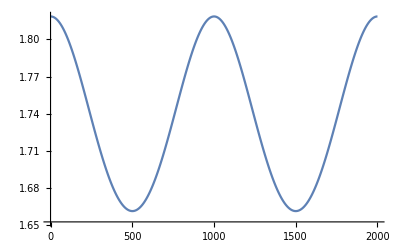

```mathematica
ListLinePlot [Values @ First @ FindRoot [Parameters["H[x,p,m]"][#,-2/(m^(1-.5)),m],{m,1}]& /@Table[i,{i,0,1,1/2000}]]
```

j from critical cong. use this in the rhs. maybe some jt is now defined and changes the value of that initial j. so, if we use the association to update the solution rules, we will alwas retrieve the most up - to - date values.